```mathematica
$packageDir = "~/Documents/IDrive-Sync/Work/Delft/Projects/Purification/Simulations/QSIM"
Needs["QSIM`basicfunctions`",FileNameJoin[{$packageDir,"QSIM_basicFunctions.m"}]]
Needs["QSIM`measurement`",FileNameJoin[{$packageDir,"QSIM_measurement.m"}]]
Needs["QSIM`stabilizers`",FileNameJoin[{$packageDir,"QSIM_stabilizers.m"}]]
Needs["QSIM`nonlocal`",FileNameJoin[{$packageDir,"QSIM_nonlocal.m"}]]
Needs["QSIM`noise`",FileNameJoin[{$packageDir,"QSIM_noise.m"}]]
Needs["QSIM`superoperators`",FileNameJoin[{$packageDir,"QSIM_superoperators.m"}]]
Needs["QSIM`errorAnalysis`",FileNameJoin[{$packageDir,"QSIM_errorAnalysis.m"}]]
```

~/Documents/IDrive-Sync/Work/Delft/Projects/Purification/Simulations/QSIM

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 

pd - the probability that a photon emitted is detected pd = pZPL*pDetect where: 
	- pZPL - probability that a given photon is in the zero photon line
	- pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>

(or can treat the raw state as being werner state in which case we need only the fidelity: 
fid - The fidelity of the raw state immediately after it is generated if there was no photon loss) 



The parameters of the distillation procedure:

pCNOT - the error rate when a CNOT gate can be performed between electron and nuclear qubits
pSWAP - the error rate when a SWAP operation is performed between electron and nuclear qubits
pmBright - the probability of error in measuring the bright state
pmDark - the probability of error in measureing the dark state
pp - the probability for a phase error between the genration of raw state 1 & 2


-----------------------------------------------
	Additional parameters
-----------------------------------------------
pCarbonDephasing - the probability for a phase error on the stored carbon state
RndOpticalPhase - the phase imprinted on the first raw state (this parameter is only just to check the robustness of the protocol





the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pZPL_,pDetect_,pDC_]:=Module[{p00,p01,p11,pd},
pd = pZPL*pDetect;
p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = 2(Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd+ 2*pDC*(1-pDC)*(1-pd));
p11 = Sin[theta]^4 *((1-pDC)^2*2*(pd *(1-pd)) + 2(1-pDC)*pDC*(1-pd)^2);

{p00,p01,p11}/(p00+p01+p11)
]

rValueAsym[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd1));

{p00,p01,p10,p11}/(p00+p01+p10+p11)
]
```

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

### Raw state generation

```mathematica
rawState[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[one,one]+rValue[[2]]*0.5*{{1-fz,0,0,0},{0,fz,-vis*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Exp[-ⅈ*RndOpticalPhase],fz,0},{0,0,0,1-fz}}+rValue[[3]]*KP[zero,zero]];

rawStateAsym[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[one,one]+{{(1-fz)(rValue[[2]]+rValue[[3]])/2,0,0,0},{0,rValue[[2]]*fz,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[-ⅈ*RndOpticalPhase],rValue[[3]]*fz,0},{0,0,0,(1-fz)(rValue[[2]]+rValue[[3]])/2}}+rValue[[4]]*KP[zero,zero]];
```

```mathematica
rawStateAsym[Sqrt[0.72],0.99,rValueAsym[π/4,0.0012,0.0006,1*^-7],0.5π]//TableForm
rawStateAsym[Sqrt[0.72],0.99,rValueAsym[π/8,0.0012,0.0006,1*^-7],0.5π]//TableForm
```

0.502245 | 0 | 0 | 0
0 | 0.165084 | 0.-0.198085 ⅈ | 0
0 | 0.+0.198085 ⅈ | 0.330114 | 0
0 | 0 | 0 | 0.00255657

0.150518 | 0 | 0 | 0
0 | 0.281586 | 0.-0.337875 ⅈ | 0
0 | 0.+0.337875 ⅈ | 0.563078 | 0
0 | 0 | 0 | 0.00481839

### EPL protocol

```mathematica
eplFromRawState[inputState_,inputState2_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_]:=Module[{rawState,rawState1,rawState2,state,cz1,cz2,hads,p,swap1,swap2},

rawState = inputState;
(*the state gets swapped onto nuclear spins *)
state = KP[rawState,zero,zero];
swap1 = twoQgate[4,1,3,swap];
swap2 = twoQgate[4,2,4,swap];
state = swap1.state.CT[swap1];
state = swap2.state.CT[swap2];
state = applyGateNoise[state,pSWAP,1,3];
state = applyGateNoise[state,pSWAP,2,4];

(*the electron spins are measured out in the zero state: NB this is post selective *)
rawState1 = measureOutcomeReal[state,{0,0},pmDark];

(* generate another raw pair on the electrons, this time there's some phase shift pp from the first one *)
rawState2 = (1-pp)*inputState2 + pp*KP[pZ,id].inputState2.KP[pZ,id];

(*dephasing of the stored state is modelled symmetrically for both nuclear spins*)
rawState1 = (1-pCarbonDephasing)^2*rawState1 + pCarbonDephasing*(1-pCarbonDephasing)*KP[pZ,id].rawState1.KP[pZ,id]+pCarbonDephasing*(1-pCarbonDephasing)*KP[id,pZ].rawState1.KP[id,pZ]+pCarbonDephasing^2*KP[pZ,pZ].rawState1.KP[pZ,pZ];

state=KP[rawState1,rawState2];

cz1=twoQgate[4,1,3,cnotB];
cz2=twoQgate[4,2,4,cnotB];

state=cz1.state.CT[cz1];
state=cz2.state.CT[cz2];

state=applyGateNoise[state,pCNOT,1,3];
state=applyGateNoise[state,pCNOT,2,4];

state=measureOutcomeReal[state,{1,1},pmDark];


state= KP[pX,id].state.KP[pX,id];


Chop[state/Tr[state]]


]
```

```mathematica
eplRotatedFromRawState[inputState_,inputState2_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_]:=Module[{rootY,rawState,rawState1,rawState2,state,cz1,cz2,hads,p,swap1,swap2},

rawState = inputState;
(*the state gets swapped onto nuclear spins *)
rootY = MatrixExp[-ⅈ*pY*π/4]; 
state = KP[rawState,zero,zero];
swap1 = twoQgate[4,1,3,swap];
swap2 = twoQgate[4,2,4,swap];
state = swap1.state.CT[swap1];
state = swap2.state.CT[swap2];
state = applyGateNoise[state,pSWAP,1,3];
state = applyGateNoise[state,pSWAP,2,4];

(*the electron spins are measured out in the zero state: NB this is post selective *)
rawState1 = measureOutcomeReal[state,{0,0},pmDark];
rawState1 = KP[rootY,rootY].rawState1.KP[rootY†,rootY†];

(* generate another raw pair on the electrons, this time there's some phase shift pp from the first one *)
(* now also supporting a different theta angle *)
(*rawState  = inputState2;*)
rawState2 = (1-pp)*inputState2 + pp*KP[pZ,id].inputState2.KP[pZ,id];

(*dephasing of the stored state is modelled symmetrically for both nuclear spins*)
rawState1 = (1-pCarbonDephasing)^2*rawState1 + pCarbonDephasing*(1-pCarbonDephasing)*KP[pZ,id].rawState1.KP[pZ,id]+pCarbonDephasing*(1-pCarbonDephasing)*KP[id,pZ].rawState1.KP[id,pZ]+pCarbonDephasing^2*KP[pZ,pZ].rawState1.KP[pZ,pZ];
rawState1 = KP[rootY†,rootY†].rawState1.KP[rootY,rootY];
state = KP[rawState1,rawState2];
(*For debugging
Print["rawstate1"];
Print[rawState1//MatrixForm];
Print["rawstate2"];
Print[rawState2//MatrixForm];
Print["PTr over qubits 1,2 of state"];
Print[(measureOutcome[state,{0,0}]+measureOutcome[state,{1,0}]+measureOutcome[state,{0,1}]+measureOutcome[state,{1,1}])//MatrixForm]; *)
cz1=twoQgate[4,1,3,cnotB];
cz2=twoQgate[4,2,4,cnotB];

state=cz1.state.CT[cz1];
state=cz2.state.CT[cz2];

state=applyGateNoise[state,pCNOT,1,3];
state=applyGateNoise[state,pCNOT,2,4];

state=measureOutcomeReal[state,{1,1},pmDark];


state= KP[pX,id].state.KP[pX,id];
(*Print[(Chop[state/Tr[state]])//MatrixForm];*)
Chop[state/Tr[state]]
]
```

```mathematica
outputState[theta_,theta2_,pZPL_,pDetect_,pDC_,vis_,fz_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_,RndOpticalPhase_,PsiPlus_:True]:=Module[{rawstate,rval,rawstate2,rval2},

rval=rValue[theta,pZPL,pDetect,pDC];
rval2 = rValue[theta2,pZPL,pDetect,pDC];

rawstate = rawState[vis,fz,rval,RndOpticalPhase];

rawstate2 =If[PsiPlus==True,rawState[vis,fz,rval2,RndOpticalPhase],rawState[-vis,fz,rval2,RndOpticalPhase]];

eplFromRawState[rawstate,rawstate2,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing]
]
```

```mathematica
outputStateRotated[theta_,theta2_,pDetect1_,pDetect2_,pDC_,vis_,fz_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_,RndOpticalPhase_,PsiPlus_:True]:=Module[{rawstate,rval,rawstate2,rval2},

rval=rValueAsym[theta,pDetect1,pDetect2,pDC];
rval2 = rValueAsym[theta2,pDetect1,pDetect2,pDC];

rawstate = rawStateAsym[vis,fz,rval,RndOpticalPhase];
rawstate2 =If[PsiPlus==True,rawStateAsym[vis,fz,rval2,RndOpticalPhase],rawStateAsym[-vis,fz,rval2,RndOpticalPhase]];

eplRotatedFromRawState[rawstate,rawstate2,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing]
]
```

## Calculate output fidelity

```mathematica
corrs[theta_,pCarbonDephasing_:0.1,pp_:0.0,RndOpticalPhase_:0.25π,PsiPlus_:True]:=Module[{pCNOT,pSWAP,pmDark,pmBright,vis,fz,pDetect1,pDetect2,pDC,outSt,outStXX,outStYY,XX,YY,ZZ,Fid,rootX,rootY},
(*RndOpticalPhase=0.25π;(*This gives the avg value*)*)
pCNOT=0.05;
pSWAP = 0.1;
pmDark = 0.01;
pmBright = 0.1;
vis =Sqrt[0.72];
fz = 0.99;
pDetect1 = 0.0012;
pDetect2 = 0.0006;
pDC=2*10^-6;

outSt=outputStateRotated[theta,theta,pDetect1,pDetect2,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase,PsiPlus];
ZZ=(outSt[[1,1]]+outSt[[4,4]]);
rootX = MatrixExp[-ⅈ*pX*π/4];
rootY = MatrixExp[-ⅈ*pY*π/4];
outStXX= KP[rootY†,rootY†].outSt.KP[rootY†,rootY†]†;
outStYY= KP[rootX,rootX].outSt.KP[rootX,rootX]†;

If[PsiPlus==True,
XX=Re@(outStXX[[1,1]]+outStXX[[4,4]]);
YY=Re@(outStYY[[2,2]]+outStYY[[3,3]]);
Fid=Re@Fidelity[outSt,bellState[0]];,
XX=Re@(outStXX[[2,2]]+outStXX[[3,3]]);YY=Re@(outStYY[[1,1]]+outStYY[[4,4]]);Fid=Re@Fidelity[outSt,bellState[3]];];
{2(XX-0.5),2(ZZ-0.5),Fid}(*Returns PARITY*)
]
```

### Fitting to data

#### Single qubit errors

How do probabilities relate to measured taus?

Lets look at an X state, and how it decoheres

```mathematica
initState={{1/2,1/2},{1/2,1/2}};
ρBlochSph[r_]:=(id+r pX)/2
DephasedState[ρ_,pFlip_]:=(1-pFlip)ρ+pFlip pZ.ρ.pZ
Purity[ρ_]:=Tr[MatrixPower[ρ,2]]
FidelityWX=Tr[initState.ρBlochSph[r]]
```

1/2+r/2

```mathematica
DephasedState[initState,p]//FullSimplify
ρBlochSph[r]/.r->(1-2p)//Simplify
```

{{1/2,-9/2},{-9/2,1/2}}

{{1/2,-9/2},{-9/2,1/2}}

Therefore the Bloch vector length r is equivalent to (1-2p). And so it follows that if r=Exp[-n/tau], p=(1-Exp[-n/tau])/2

```mathematica
(*1-Sum[Binomial[n,2k] p^(2k)(1-p)^(n-2k),{k,0,n/2}]/.p->(1-Exp[-1/tau])/2//FullSimplify Consistent with my previous model. P per single shot is (1-Exp[-1/tau])/2*)
```

```mathematica
PDephased[tau_,n_]:=(1-Exp[-(n/tau)])/2;(*Derived from Sum[Binomial[n,2k] p^(2k)(1-p)^(n-2k),{k,0,n/2}]*)
```

#### Two qubit gate errors

```mathematica
state = KP[initState,zero];
state = swap.state.CT[swap];
state = applyGateNoise[state,pNoise,1,2];
state = swap.state.CT[swap];
state = applyGateNoise[state,pNoise,1,2];
state=TraceSystem[state,{2}];
fid=Fidelity[state,initState]
```

2 (1/2-(8 pNoise)/15+(64 pNoise^2)/225)

```mathematica
Solve[{fid==0.90,pNoise<1},pNoise]
```

{{pNoise→0.0989745}}

#### Phase flips

What about phase flips between the states?

```mathematica
phasePerAttempt=0.05π /Sqrt[3/0.007];
pFlipPerAttempt=Sin[phasePerAttempt]^2;
```

Phase flips are pretty much irrelevant

```mathematica
(*corrsTab=Table[{θ,corrs[π/8,PDephased[tauDephasingXY,400],0,θ]},{θ,0,2π,π/10}];
ListPlot[Table[{corrsTab[[k,1]],corrsTab[[k,2,i]]},{i,1,3},{k,1,Dimensions[corrsTab][[1]]}]]*)
```

#### Phase compensation uncertainty

Pick up a slight unknown phase after every attempt since calibration not perfect.

```mathematica
coherences=Integrate[1/(√(2π)Δθ)Exp[-(δθ^2/(2 Δθ^2))] ⅇ^(ⅈ reps δθ),{δθ,-∞,∞},Assumptions->{Δθ>0}]
```

ⅇ^(-1/2 reps^2 Δθ^2)

So block vector length goes as ⅇ^(-1/2 reps^2 Δθ^2), therefore p=(1-ⅇ^(-1/2 n^2 Δθ^2))/2

```mathematica
pLossOfPhase[n_,Δθ_]:=(1-ⅇ^(-1/2 n^2 Δθ^2))/2
```

#### Combining the two processes (phase uncertainty and decoherence)

```mathematica
pCombined[n_,Δθ_,tau_]:=(1-ⅇ^(-1/2 n^2 Δθ^2-n/tau))/2
```

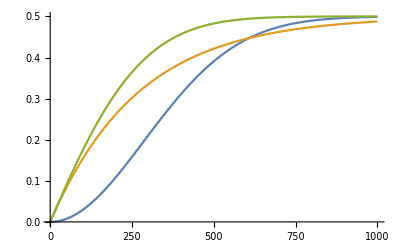

```mathematica
tauDephasingXY=270.; 
phaseUncertaintyPerAttempt =(0.2/180)π;
Plot[{pLossOfPhase[n,phaseUncertaintyPerAttempt],PDephased[tauDephasingXY,n],pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]},{n,1,1000}]
```

### Modelling

```mathematica
tauDephasingXY=270.; 
phaseUncertaintyPerAttempt =0.2π/180;
```

```mathematica
basePath="/Users/humphreys/Repositories/personal_calcs/Work/Modelling/Purification/MeasuredFidelities";
```

#### π/4

```mathematica
theta =π/4;
binSize=50;
maxAttempts=450;
```

```mathematica
dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[theta,InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
ZZ=data[[;;,1]];
YY=data[[;;,2]];
XX=data[[;;,3]];
ZZu=data[[;;,4]];
YYu=data[[;;,5]];
XXu=data[[;;,6]];
Fid=(ZZ+YY+XX+1)/4;
Fidu=Sqrt[ZZu^2+YYu^2+XXu^2]/4;
bins =Table[n,{n,binSize,maxAttempts,binSize}];
```

```mathematica
OutcomeCorrs=Table[corrs[theta,pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]],{n,1,maxAttempts}];
OutcomeCorrsToPlot=Table[{n,OutcomeCorrs[[n,i]]},{i,1,3},{n,1,maxAttempts}];
binnedOutcomeCorrs=Table[{n,Sum[OutcomeCorrs[[k,i]],{k,n-binSize+1,n}]/binSize},{i,1,2},{n,binSize,maxAttempts,binSize}];
binnedOutcomeFid=Table[{n,Sum[OutcomeCorrs[[k,3]],{k,n-binSize+1,n}]/binSize},{n,binSize,maxAttempts,binSize}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

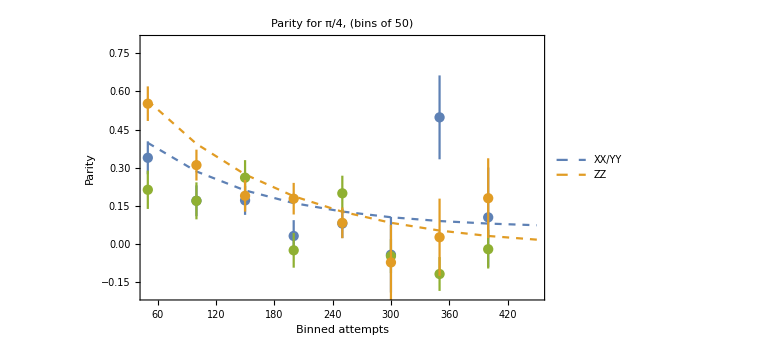

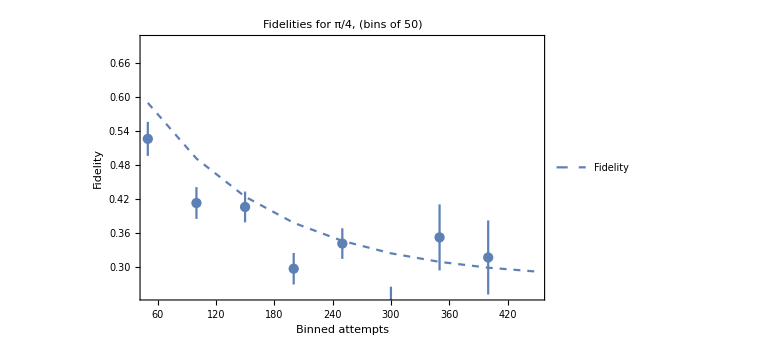

```mathematica
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];

originalCorrs=ListPlot[OutcomeCorrsToPlot,PlotRange->All,Joined->True,PlotLabel->StringForm["``",theta,InputForm],PlotLegends->{"XX","YY","Fidelity"}];
modelledCorrs=ListPlot[binnedOutcomeCorrs,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Parity for ``, (bins of ``)",theta,binSize,InputForm],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"XX/YY","ZZ"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Parity"}];
modelledFid=ListPlot[binnedOutcomeFid,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Fidelity"}];


XXPlot=ErrorListPlot[Table[{{bins[[i]],XX[[i]]},ErrorBar[XXu[[i]]]},{i,1,Length[XX]}],PlotStyle->ColorData[97,"ColorList"][[1]]];
YYPlot=ErrorListPlot[Table[{{bins[[i]],YY[[i]]},ErrorBar[YYu[[i]]]},{i,1,Length[YY]}],PlotStyle->ColorData[97,"ColorList"][[3]]];
ZZPlot=ErrorListPlot[Table[{{bins[[i]],ZZ[[i]]},ErrorBar[ZZu[[i]]]},{i,1,Length[ZZ]}],PlotStyle->ColorData[97,"ColorList"][[2]]];
FidPlot=ErrorListPlot[Table[{{bins[[i]],Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

#### π/5

```mathematica
theta =π/5;
binSize=50;
maxAttempts=450;
```

```mathematica
dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[theta,InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
ZZ=data[[;;,1]];
YY=data[[;;,2]];
XX=data[[;;,3]];
ZZu=data[[;;,4]];
YYu=data[[;;,5]];
XXu=data[[;;,6]];
Fid=(ZZ+YY+XX+1)/4;
Fidu=Sqrt[ZZu^2+YYu^2+XXu^2]/4;
bins =Table[n,{n,binSize,maxAttempts,binSize}];
```

```mathematica
OutcomeCorrs=Table[corrs[theta,pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]],{n,1,maxAttempts}];
OutcomeCorrsToPlot=Table[{n,OutcomeCorrs[[n,i]]},{i,1,3},{n,1,maxAttempts}];
binnedOutcomeCorrs=Table[{n,Sum[OutcomeCorrs[[k,i]],{k,n-binSize+1,n}]/binSize},{i,1,2},{n,binSize,maxAttempts,binSize}];
binnedOutcomeFid=Table[{n,Sum[OutcomeCorrs[[k,3]],{k,n-binSize+1,n}]/binSize},{n,binSize,maxAttempts,binSize}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

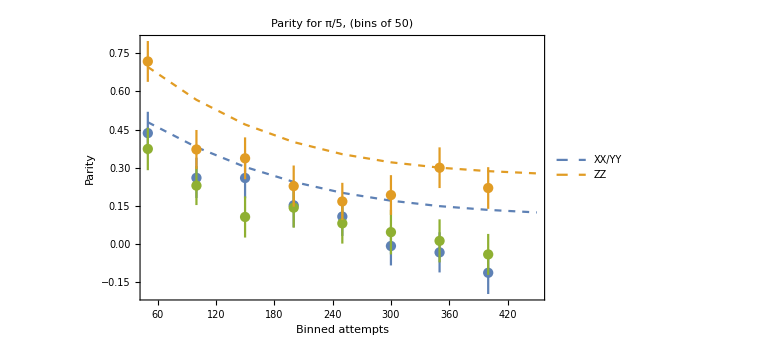

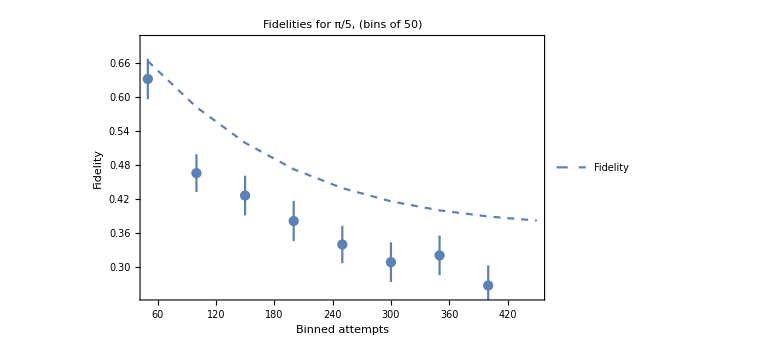

```mathematica
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];

originalCorrs=ListPlot[OutcomeCorrsToPlot,PlotRange->All,Joined->True,PlotLabel->StringForm["``",theta,InputForm],PlotLegends->{"XX","YY","Fidelity"}];
modelledCorrs=ListPlot[binnedOutcomeCorrs,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Parity for ``, (bins of ``)",theta,binSize,InputForm],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"XX/YY","ZZ"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Parity"}];
modelledFid=ListPlot[binnedOutcomeFid,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Fidelity"}];


XXPlot=ErrorListPlot[Table[{{bins[[i]],XX[[i]]},ErrorBar[XXu[[i]]]},{i,1,Length[XX]}],PlotStyle->ColorData[97,"ColorList"][[1]]];
YYPlot=ErrorListPlot[Table[{{bins[[i]],YY[[i]]},ErrorBar[YYu[[i]]]},{i,1,Length[YY]}],PlotStyle->ColorData[97,"ColorList"][[3]]];
ZZPlot=ErrorListPlot[Table[{{bins[[i]],ZZ[[i]]},ErrorBar[ZZu[[i]]]},{i,1,Length[ZZ]}],PlotStyle->ColorData[97,"ColorList"][[2]]];
FidPlot=ErrorListPlot[Table[{{bins[[i]],Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

#### π/6

```mathematica
theta =π/6;
binSize=50;
maxAttempts=450;
```

```mathematica
dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[theta,InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
ZZ=data[[;;,1]];
YY=data[[;;,2]];
XX=data[[;;,3]];
ZZu=data[[;;,4]];
YYu=data[[;;,5]];
XXu=data[[;;,6]];
Fid=(ZZ+YY+XX+1)/4;
Fidu=Sqrt[ZZu^2+YYu^2+XXu^2]/4;
bins =Table[n,{n,binSize,maxAttempts,binSize}];
```

```mathematica
OutcomeCorrs=Table[corrs[theta,pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]],{n,1,maxAttempts}];
OutcomeCorrsToPlot=Table[{n,OutcomeCorrs[[n,i]]},{i,1,3},{n,1,maxAttempts}];
binnedOutcomeCorrs=Table[{n,Sum[OutcomeCorrs[[k,i]],{k,n-binSize+1,n}]/binSize},{i,1,2},{n,binSize,maxAttempts,binSize}];
binnedOutcomeFid=Table[{n,Sum[OutcomeCorrs[[k,3]],{k,n-binSize+1,n}]/binSize},{n,binSize,maxAttempts,binSize}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

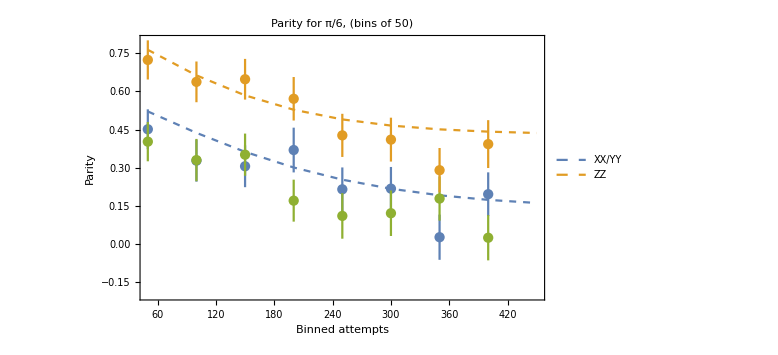

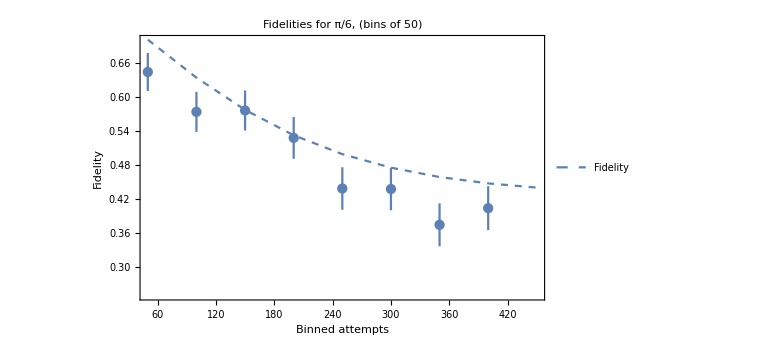

```mathematica
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];

originalCorrs=ListPlot[OutcomeCorrsToPlot,PlotRange->All,Joined->True,PlotLabel->StringForm["``",theta,InputForm],PlotLegends->{"XX","YY","Fidelity"}];
modelledCorrs=ListPlot[binnedOutcomeCorrs,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Parity for ``, (bins of ``)",theta,binSize,InputForm],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"XX/YY","ZZ"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Parity"}];
modelledFid=ListPlot[binnedOutcomeFid,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Fidelity"}];


XXPlot=ErrorListPlot[Table[{{bins[[i]],XX[[i]]},ErrorBar[XXu[[i]]]},{i,1,Length[XX]}],PlotStyle->ColorData[97,"ColorList"][[1]]];
YYPlot=ErrorListPlot[Table[{{bins[[i]],YY[[i]]},ErrorBar[YYu[[i]]]},{i,1,Length[YY]}],PlotStyle->ColorData[97,"ColorList"][[3]]];
ZZPlot=ErrorListPlot[Table[{{bins[[i]],ZZ[[i]]},ErrorBar[ZZu[[i]]]},{i,1,Length[ZZ]}],PlotStyle->ColorData[97,"ColorList"][[2]]];
FidPlot=ErrorListPlot[Table[{{bins[[i]],Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

#### π/8

```mathematica
theta =π/8;
binSize=50;
maxAttempts=450;
```

```mathematica
dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[theta,InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
ZZ=data[[;;,1]];
YY=data[[;;,2]];
XX=data[[;;,3]];
ZZu=data[[;;,4]];
YYu=data[[;;,5]];
XXu=data[[;;,6]];
Fid=(ZZ+YY+XX+1)/4;
Fidu=Sqrt[ZZu^2+YYu^2+XXu^2]/4;
bins =Table[n,{n,binSize,maxAttempts,binSize}];
```

```mathematica
OutcomeCorrs=Table[corrs[theta,pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]],{n,1,maxAttempts}];
OutcomeCorrsToPlot=Table[{n,OutcomeCorrs[[n,i]]},{i,1,3},{n,1,maxAttempts}];
binnedOutcomeCorrs=Table[{n,Sum[OutcomeCorrs[[k,i]],{k,n-binSize+1,n}]/binSize},{i,1,2},{n,binSize,maxAttempts,binSize}];
binnedOutcomeFid=Table[{n,Sum[OutcomeCorrs[[k,3]],{k,n-binSize+1,n}]/binSize},{n,binSize,maxAttempts,binSize}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

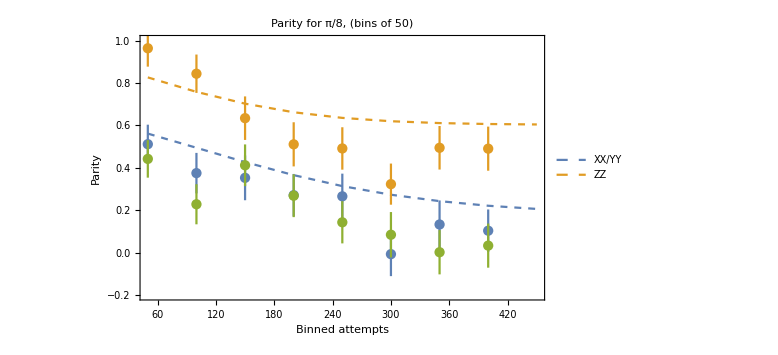

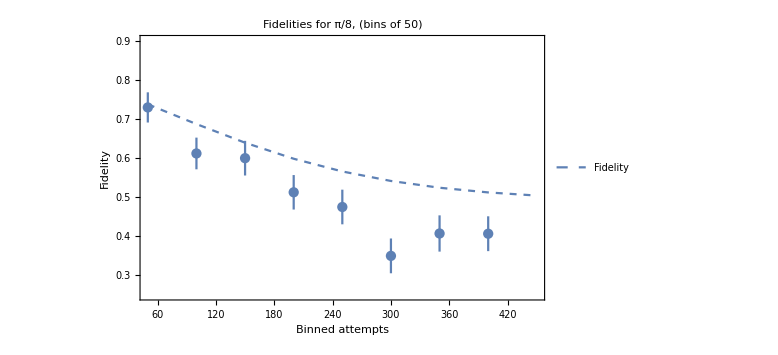

```mathematica
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];

originalCorrs=ListPlot[OutcomeCorrsToPlot,PlotRange->All,Joined->True,PlotLabel->StringForm["``",theta,InputForm],PlotLegends->{"XX","YY","Fidelity"}];
modelledCorrs=ListPlot[binnedOutcomeCorrs,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Parity for ``, (bins of ``)",theta,binSize,InputForm],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"XX/YY","ZZ"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Parity"}];
modelledFid=ListPlot[binnedOutcomeFid,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Fidelity"}];


XXPlot=ErrorListPlot[Table[{{bins[[i]],XX[[i]]},ErrorBar[XXu[[i]]]},{i,1,Length[XX]}],PlotStyle->ColorData[97,"ColorList"][[1]]];
YYPlot=ErrorListPlot[Table[{{bins[[i]],YY[[i]]},ErrorBar[YYu[[i]]]},{i,1,Length[YY]}],PlotStyle->ColorData[97,"ColorList"][[3]]];
ZZPlot=ErrorListPlot[Table[{{bins[[i]],ZZ[[i]]},ErrorBar[ZZu[[i]]]},{i,1,Length[ZZ]}],PlotStyle->ColorData[97,"ColorList"][[2]]];
FidPlot=ErrorListPlot[Table[{{bins[[i]],Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,1.0}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.9}},AxesOrigin->{0,0.25},ImageSize->Large]
```

### Function of theta

```mathematica
thetas={π/4,π/5,π/6,π/8};
```

```mathematica
binSize=50;
FidVsTheta=Table[{Sin[theta]^2,Sum[corrs[theta,pCombined[n,phaseUncertaintyPerAttempt,tauDephasingXY]][[3]],{n,1,binSize}]/binSize},{theta,0,π/2,π/20}];
```

```mathematica
Fid={};
Fidu={};
For[i=1,i≤Dimensions[thetas][[1]],i++,
dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[thetas[[i]],InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
ZZ=data[[1,1]];
YY=data[[1,2]];
XX=data[[1,3]];
ZZu=data[[1,4]];
YYu=data[[1,5]];
XXu=data[[1,6]];
Fid=Append[Fid,(ZZ+YY+XX+1)/4];
Fidu=Append[Fidu,Sqrt[ZZu^2+YYu^2+XXu^2]/4];]
```

```mathematica
Needs["ErrorBarPlots`"]
```

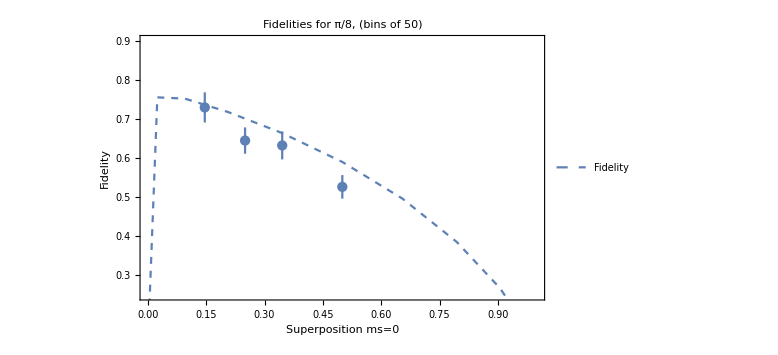

```mathematica
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];

modelledFid=ListPlot[FidVsTheta,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Superposition ms=0","Fidelity"}];

FidPlot=ErrorListPlot[Table[{{Sin[thetas[[i]]]^2,Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.9}},AxesOrigin->{0,0.25},ImageSize->Large]
```

```mathematica
Reverse[Fid]
Reverse[Fidu]
```

{0.729154,0.644452,0.632045,0.526112}

{0.0385802,0.0335684,0.0357766,0.0300881}

```mathematica
Print[FidVsTheta[[;;,1]]//N]
Print[FidVsTheta[[;;,2]]//N]
```

{0.,0.0244717,0.0954915,0.206107,0.345492,0.5,0.654508,0.793893,0.904508,0.975528,1.}

{0.116475,0.75495,0.751584,0.717445,0.663532,0.589792,0.496099,0.385553,0.268143,0.164567,0.116475}